# Construct k⃗·P̂ Models for Semiconductors

kaifaluo@outlook.com

## 1, Quick Review of Symmetries in QM

### 1.1 Symmetry Groups of Crystals

Ĥ=∑_k ((ĉ)_k)^†h(k)(ĉ)_k
Ŝ Ĥ (Ŝ)^-1=Ĥ→ S h(k⃗)S^-1=h(S k⃗), S=[Ŝ]_ψ
G_(k⃗)={g∈G|g h(k⃗)g^-1=h(g k⃗)} → Little group at k⃗ point, an invariant subgroup of the space group G

8 independent symmorphic operators:
1,2,3,4,6,OverBar[4],ⅈ,m
OverBar[4]=ⅈ C_4,m_[u,v,w]=ⅈ C_(2,[u,v,w]) ⇒ (Ĉ)_(n,r̂)=e^(-ⅈ (2π)/n Ĵ·r̂),ⅈ,T̂ (n=1,2,3,4,6)

### 1.2 Atomic Orbitals

#### 1.2.1 spinless orbitals: s,p_(x,y,z), E_g, T_(2g), ⋯

ψ=(ψ_1,ψ_2,⋯,ψ_N)^T, ψ_i=Y_(l_i m_i);
g_i ψ_1
ψ_2
⋮
ψ_N=ψ_1'
ψ_2'
⋮
ψ_N'=M_(N×N)ψ_1
ψ_2
⋮
ψ_N⇒ [g_i]_ψ=M_(N×N);
T̂=K;

#### 1.2.2 SOC included: |j,m⟩,|j_1,m_1;1/2,±1/2⟩

(J_(+,z))_αβ= ⟨j_α,m_α|(Ĵ)_(+,z)|j_β,m_β⟩,J_-=(J_+)^†
(Ĵ)_+|j,m⟩=ℏ √(j(j+1)-m(m+1))|j,m+1⟩(m+1≤ j)

 (Ĉ)_(n,[u v w])=e^(-ⅈ (2π)/(n √(u^2+v^2+w^2))(u J_x+v J_y+w J_z))=e^(-ⅈ (2π)/(n √(u^2+v^2+w^2))[u/2(J_++J_-)+v/(2ⅈ)(J_+-J_-)+w J_z])
T̂=e^(-ⅈπ (Ĵ)_y)K

refs：
喀兴林，高等量子力学，Ch-2.8;
C. Cohen-Tannoudji, Quantum Mechanics, Ch-6;
Bernevig, Topological Insulators and Topological Superconductors, Ch-4.

### 1.3 k·p perturbation term

((p̂)^2/(2m)+V(r⃗)+ℏ/(4 m^2 c^2)(σ⃗×∇V)·p̂)ψ_(n,k⃗)(r⃗)=E_(n,k⃗)ψ_(n,k⃗)(r⃗)
⟶^(ψ_(n,k⃗)(r⃗)=e^(ⅈ k⃗·r⃗)u_(n,k⃗)(r⃗))[(Ĥ)_((k⃗)_0)+(Ĥ)_kp]u_(n,(k⃗)_0+k⃗)(r⃗)=(E_(n,(k⃗)_0+k⃗)-((ℏ^2((k⃗)_0+k⃗))^2)/(2m))u_(n,(k⃗)_0+k⃗)(r⃗)
where  (Ĥ)_kp=ℏ/m k⃗·P̂=ℏ/(2m)(k_+(P̂)_-+k_-(P̂)_+)+ℏ/m k_z(P̂)_z,  where P̂=p̂+ℏ/(4 m^2 c^2)(σ×∇V)

H=ϵ_(1,(k̂)_0) | 0 | 0 | 0
0 | ϵ_(2,(k̂)_0) | 0 | 0
0 | 0 | ⋱ | 0
0 | 0 | 0 | ϵ_(N,(k̂)_0) + [(Ĥ)_(kp,(k⃗)_0)]_ψ;
Our task: [(Ĥ)_(kp,(k⃗)_0)]_ψ satisfying the symmetry group G_((k⃗)_0)

refs:
谢希德，固体能带理论，Ch-3.2;
R. Yu et al, New J. Phys. 17(2015) 023012, Model Hamiltonian for topological Kondo insulator SmB_6.

### 1.4, Some Properties of Point Groups: Irreps & Character Tables

-Graphics-
-Graphics--Graphics-
-Graphics-

refs :
  喀兴林，高等量子力学，p262; 
  喀兴林，群论及其在固体物理中的应用，ch - 2 群表示理论; 
  Bilbao : http : // www.cryst.ehu.es/

### 1.5, Step-by-step Overview

-Graphics-

### 1.5, FAQs

#### Q1, What if minimum orbitals are hard to be grouped as a ECOC?

Quasi-degenerate perturbation theory

refs: 
Roland Walker, Spin–Orbit Coupling Effects in Two-Dimensional Electron and Hole Systems, Appendix B;
CC Liu et al, PRB 84, 195430(2011), Low-energy effective Hamiltonian involving spin-orbit coupling in silicene and two-dimensional germanium and tin.

#### Q2, How to estimate the influence of the SOC term?

#### Q2.1 SOC of atomic orbitals (spherical symmetry)

H_so=ξ(r)L̂·Ŝ=ξ(r)[1/2((L̂)_-(Ŝ)_++(L̂)_+(Ŝ)_-)+(Ŝ)_z(L̂)_z]=ξ(r)(L̂)_z | 1/2(L̂)_+
1/2(L̂)_- | -(L̂)_z;  (* Ψ=(ψ_↑,ψ_↓)^T *)
refs:
M.D. Jones and R.C. Albers, PRB 79, 045107(2009), Spin-orbit coupling in an f-electron tight-binding model: Electronic properties of Th, U, and Pu

#### Q2.2 Rashba SOC, Dresselhaus SOC

H_D_3^(Γ)=(γ/ℏ)[(p_y^2-p_z^2)p_x σ_x+c.p.]  
(* zinc-blende III-V semiconductor compounds lacking a centre of inversion *)

H_R=(α_R/ℏ)(z⃗×p̂)·σ⃗
(* In quantum well with structural inversion broken along z⃗-direction, resulted by interfacial E⃗ *)

refs:
A. Manchon et al, Nat. Materials 14, 871(2015), New perspectives for Rashba spin-orbit coupling;
C.L. Kane and E.J. Mele, PRL 95, 226801(2005), Quantum Spin Hall Effect in Graphene;
M.S. Dresselhaus, Springer(2008), Group Theory: Application to the Physics of Condensed Matter, Ch 14.

#### Q2.3 From definition of SOC term

H_so=ℏ/(4 m_0^2 c^2)(∇V×p⃗)·σ⃗=-ℏ/(4 m_0^2 c^2)(F⃗×p⃗)·σ⃗

-Graphics-

refs:
C.C. Liu et al, PRB 84, 195430(2011), Low-energy effective Hamiltonian involving spin-orbit coupling in silicene and two-dimensional germanium and tin;
R. Yu et al, PRL 119, 036401(2017), From Nodal Chain Semimetal to Weyl Semimetal in HfC, Supplemental Materials

### Q3, What if the k⃗ points is at the boundary of BZ?

We have to find the reps of Space Groups.

## Example 1: D_(4h)+s p_(x y z) (Cd_3 As_2)

### 1.0 Basis & Reps of Generators

-Graphics-
C_(2z) conserve the secondary angular momentum up to 2;
g_2 s
p_+
p_-
p_z=g_2 s
-p_x-ⅈp_y
p_x-ⅈp_y
p_z=s
p_y-ⅈp_x
-p_y-ⅈp_x
p_z=s
ⅈp_+
-ⅈp_-
p_z⇒C_(4z)=g_2=1 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | 1;
g_3 s
p_+
p_-
p_z=g_3 s
-p_x-ⅈp_y
p_x-ⅈp_y
p_z=s
p_x-ⅈp_y
-p_x-ⅈp_y
-p_z=s
p_-
p_+
-p_z⇒C_(2y)=g_3=1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | -1;
P=g_4=1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1;

### 1.1 Write the initial k.p model and Input all reps

```mathematica
ClearAll["Global`*"];
(*basis: S, S, P, P*)
es = e10 + e11 kp km + e12 kz kz + e13 km km + e13s kp kp;
ex = e20 + e21 kp km + e22 kz kz + e23 km km + e23s kp kp;
ey = e30 + e31 kp km + e32 kz kz + e33 km km + e33s kp kp;
ez = e40 + e41 kp km + e42 kz kz + e43 km km + e43s kp kp;
H1=({{es, a121 kp+a122 km, a131 kp+a132 km, a140+a141 kz}, {a121s km+a122s kp, ex, a230+a231 kz, a241 kp+a242 km}, {a131s km+a132s kp, a230s+a231s kz, ey, a341 kp+a342 km}, {a140s+a141s kz, a241s km+a242s kp, a341s km+a342s kp, ez}});
C4z={{Exp[-ⅈ(2π)/4], 0, 0, 0}, {0, Exp[ⅈ(2π)/4], 0, 0}, {0, 0, Exp[-ⅈ(2π)/4], 0}, {0, 0, 0, Exp[ⅈ(2π)/4]}};
P={{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}};
TRSO={{0, -ⅈ, 0, 0}, {ⅈ, 0, 0, 0}, {0, 0, 0, -ⅈ}, {0, 0, ⅈ, 0}};
```

### 1.2 k.p models Constrained by symmetries one by one

#### 1.2.1 TRS (-k_x,-k_y,-k_z)

```mathematica
H1t=FullSimplify[(Transpose[H1]/.{kp->-kp,km->-km,kz->-kz})-Inverse[TRSO].H1.TRSO];
Print["H1t=",MatrixForm[H1t]]
```

H1t=(e10-e20+(e13-e23) km^2+(e11-e21) km kp+(e13s-e23s) kp^2+(e12-e22) kz^2 | 0 | -(a131s+a242) km-(a132s+a241) kp | a140s+a230+(-a141s+a231) kz
0 | -e10+e20-e13 km^2+e23 km^2+kp (-e11 km+e21 km+(-e13s+e23s) kp)+(-e12+e22) kz^2 | a140+a230s+(a141-a231s) kz | -(a132+a241s) km-(a131+a242s) kp
-(a132+a241s) km-(a131+a242s) kp | a140s+a230+(a141s-a231) kz | e30-e40+(e33-e43) km^2+(e31-e41) km kp+(e33s-e43s) kp^2+(e32-e42) kz^2 | 0
a140+a230s+(-a141+a231s) kz | -(a131s+a242) km-(a132s+a241) kp | 0 | -e30+e40-e33 km^2+e43 km^2+kp (-e31 km+e41 km+(-e33s+e43s) kp)+(-e32+e42) kz^2)

```mathematica
e20=e10;e23=e13;e21=e11;e23s=e13s;e22=e12;
e40=e30;e43=e33;e41=e31;e42=e32;e43s=e33s;
a241s=-a132;a242s=-a131;a140s=-a230;a141s=a231;
a230s=-a140;a231s=a141;a131s=-a242;a132s=-a241;
Print["H1t=",MatrixForm[H1t]]
```

H1t=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

#### 1.2.2 Inversion (-k_x,-k_y,-k_z)

```mathematica
Hp=FullSimplify[(H1/.{kp->-kp,km->-km,kz->-kz})-Inverse[P].H1.P];
Print["Hp",MatrixForm[Hp]]
```

Hp(0 | -2 (a122 km+a121 kp) | 0 | 2 a140
-2 (a121s km+a122s kp) | 0 | 2 a230 | 0
0 | -2 a140 | 0 | -2 (a342 km+a341 kp)
-2 a230 | 0 | -2 (a341s km+a342s kp) | 0)

```mathematica
a140=0;a230=0;a342=0;a341=0;a121s=0;a122s=0;a122=0;a121=0;a341s=0;a342s=0;
Print["Hp=",MatrixForm[Hp],"; H1=",MatrixForm[H1]]
```

Hp=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)H1=(e10+e13 km^2+e11 km kp+e13s kp^2+e12 kz^2 | 0 | a132 km+a131 kp | a141 kz
0 | e10+e13 km^2+e11 km kp+e13s kp^2+e12 kz^2 | a231 kz | a242 km+a241 kp
-a242 km-a241 kp | a141 kz | e30+e33 km^2+e31 km kp+e33s kp^2+e32 kz^2 | 0
a231 kz | -a132 km-a131 kp | 0 | e30+e33 km^2+e31 km kp+e33s kp^2+e32 kz^2)

#### 1.2.5 Final result

```mathematica
kp=kx+ⅈ ky;
km=kx-ⅈ ky;
MatrixForm[Collect[H1,{kx,ky,kz}]]
```

(e10+(e11+e13+e13s) kx^2+(-2 ⅈ e13+2 ⅈ e13s) kx ky+(e11-e13-e13s) ky^2+e12 kz^2 | 0 | (a131+a132) kx+(ⅈ a131-ⅈ a132) ky | a141 kz
0 | e10+(e11+e13+e13s) kx^2+(-2 ⅈ e13+2 ⅈ e13s) kx ky+(e11-e13-e13s) ky^2+e12 kz^2 | a231 kz | (a241+a242) kx+(ⅈ a241-ⅈ a242) ky
(-a241-a242) kx+(-ⅈ a241+ⅈ a242) ky | a141 kz | e30+(e31+e33+e33s) kx^2+(-2 ⅈ e33+2 ⅈ e33s) kx ky+(e31-e33-e33s) ky^2+e32 kz^2 | 0
a231 kz | (-a131-a132) kx+(-ⅈ a131+ⅈ a132) ky | 0 | e30+(e31+e33+e33s) kx^2+(-2 ⅈ e33+2 ⅈ e33s) kx ky+(e31-e33-e33s) ky^2+e32 kz^2)

## Example 2: D2+s p_xyz (Ag_2S)

### 0. Band Infos and Irreducible Reps

#### 0.1 Pick dominant atomic orbitals satisfying symmetries’ constrains

(bands without spin-orbit coupling)

-Graphics--Graphics-


ψ~(Γ_1,Γ_2,Γ_1,Γ_3)^T~(s,p_y,s,p_z)^T

#### 0.2 Find the matrix reps of all generators

-Graphics-
g_1 ψ=g_1(s
p_y
s
p_z)=(s
-p_y
s
p_z)⇒g_1=(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1);(C_(2z))
g_2 ψ=g_2(s
p_y
s
p_z)=(s
p_y
s
-p_z)⇒g_2=(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1);(C_(2y))
g_3=K;(*TRS*)

### 1 Derive the k.p model

#### 1.1 Initialize the k.p Hamiltonian

```mathematica
(*magnetic angular momentum number conserve up to 2*)
(* ψ~(s,Subscript[p, y],s,Subscript[p, z])^T *)

ClearAll["Global`*"]

es1 = es10 + es11 kp km + es12 kz^2 + es13 km^2 + es13s kp^2;
es2 = es20 + es21 kp km + es22 kz^2 + es23 km^2 + es23s kp^2;
epy = epy0 + epy1 kp km + epy2 kz^2 + epy3 km^2 + epy3s kp^2;
epz = epz0 + epz1 kp km + epz2 kz^2 + epz3 km^2 + epz3s kp^2;
H1=({{es1, a121 km+a122 kp, a130+a131 kz, a141+a142 kz}, {a121s kp+a122s km, epy, a231 km+a232 kp, a241 kp+a242 km}, {a130s+a131s kz, a231s kp+a232s km, es2, a341+a342 kz}, {a141s+a142s kz, a241s km+a242s kp, a341s+a342s kz, epz}});
H2=({{0, b121 kp kz+b122 km kz, b131 kz^2+b132 kp^2+b133 km^2+b134 kp km, b141 kz^2+b142 kp^2+b143 km^2+b144 kp km}, {b121s km kz+b122s kp kz, 0, b231 kp kz+b232 km kz, b241 kp kz+b242 km kz}, {b131s kz^2+b132s km^2+b133s kp^2+b134s kp km, b231s km kz+b232s kp kz, 0, b341 kz^2+b342 kp^2+b343 km^2+b344 kp km}, {b141s kz^2+b142s km^2+b143s kp^2+b144s kp km, b241s km kz+b242s kp kz, b341s kz^2+b342s km^2+b343s kp^2+b344s kp km, 0}});
H3={{0, 0, 0, c141 kp^2 kz+c142 km^2 kz+c143 kp km kz+c144 kz^3}, {0, 0, 0, 0}, {0, 0, 0, 0}, {c141s km^2 kz+c142s kp^2 kz+c143s kp km kz+c144s kz^3, 0, 0, 0}};
```

Input all matrix reps

```mathematica
g1=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}); (* Subscript[C, 2z] *)
g2=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}); (* Subscript[C, 2y] *)
```

(H_1+H_2+H_3) is C_(2z) symmetric automatically!

```mathematica
H=H1+H2+H3;
dHC2z=(g1.H.Inverse[g1])-(H/.{kp->-kp,km->-km,kz->kz});
MatrixForm[dHC2z]
```

(-es13s (-kx-ⅈ ky)^2+es13 (kx-ⅈ ky)^2-es11 (-kx-ⅈ ky) (-kx+ⅈ ky)-es13 (-kx+ⅈ ky)^2+es11 (kx-ⅈ ky) (kx+ⅈ ky)+es13s (kx+ⅈ ky)^2 | -b121 (-kx-ⅈ ky) kz-b122 (kx-ⅈ ky) kz-b122 (-kx+ⅈ ky) kz-b121 (kx+ⅈ ky) kz | -b132 (-kx-ⅈ ky)^2+b133 (kx-ⅈ ky)^2-b134 (-kx-ⅈ ky) (-kx+ⅈ ky)-b133 (-kx+ⅈ ky)^2+b134 (kx-ⅈ ky) (kx+ⅈ ky)+b132 (kx+ⅈ ky)^2 | -b142 (-kx-ⅈ ky)^2+b143 (kx-ⅈ ky)^2-b144 (-kx-ⅈ ky) (-kx+ⅈ ky)-b143 (-kx+ⅈ ky)^2+b144 (kx-ⅈ ky) (kx+ⅈ ky)+b142 (kx+ⅈ ky)^2-c141 (-kx-ⅈ ky)^2 kz+c142 (kx-ⅈ ky)^2 kz-c143 (-kx-ⅈ ky) (-kx+ⅈ ky) kz-c142 (-kx+ⅈ ky)^2 kz+c143 (kx-ⅈ ky) (kx+ⅈ ky) kz+c141 (kx+ⅈ ky)^2 kz
-b122s (-kx-ⅈ ky) kz-b121s (kx-ⅈ ky) kz-b121s (-kx+ⅈ ky) kz-b122s (kx+ⅈ ky) kz | -epy3s (-kx-ⅈ ky)^2+epy3 (kx-ⅈ ky)^2-epy1 (-kx-ⅈ ky) (-kx+ⅈ ky)-epy3 (-kx+ⅈ ky)^2+epy1 (kx-ⅈ ky) (kx+ⅈ ky)+epy3s (kx+ⅈ ky)^2 | -a232 (-kx-ⅈ ky)-a232 (kx+ⅈ ky)-b231 (-kx-ⅈ ky) kz-b232 (kx-ⅈ ky) kz-b232 (-kx+ⅈ ky) kz-b231 (kx+ⅈ ky) kz | -b241 (-kx-ⅈ ky) kz-b242 (kx-ⅈ ky) kz-b242 (-kx+ⅈ ky) kz-b241 (kx+ⅈ ky) kz
-b133s (-kx-ⅈ ky)^2+b132s (kx-ⅈ ky)^2-b134s (-kx-ⅈ ky) (-kx+ⅈ ky)-b132s (-kx+ⅈ ky)^2+b134s (kx-ⅈ ky) (kx+ⅈ ky)+b133s (kx+ⅈ ky)^2 | -a232s (kx-ⅈ ky)-a232s (-kx+ⅈ ky)-b232s (-kx-ⅈ ky) kz-b231s (kx-ⅈ ky) kz-b231s (-kx+ⅈ ky) kz-b232s (kx+ⅈ ky) kz | -es23s (-kx-ⅈ ky)^2+es23 (kx-ⅈ ky)^2-es21 (-kx-ⅈ ky) (-kx+ⅈ ky)-es23 (-kx+ⅈ ky)^2+es21 (kx-ⅈ ky) (kx+ⅈ ky)+es23s (kx+ⅈ ky)^2 | -b342 (-kx-ⅈ ky)^2+b343 (kx-ⅈ ky)^2-b344 (-kx-ⅈ ky) (-kx+ⅈ ky)-b343 (-kx+ⅈ ky)^2+b344 (kx-ⅈ ky) (kx+ⅈ ky)+b342 (kx+ⅈ ky)^2
-b143s (-kx-ⅈ ky)^2+b142s (kx-ⅈ ky)^2-b144s (-kx-ⅈ ky) (-kx+ⅈ ky)-b142s (-kx+ⅈ ky)^2+b144s (kx-ⅈ ky) (kx+ⅈ ky)+b143s (kx+ⅈ ky)^2-c142s (-kx-ⅈ ky)^2 kz+c141s (kx-ⅈ ky)^2 kz-c143s (-kx-ⅈ ky) (-kx+ⅈ ky) kz-c141s (-kx+ⅈ ky)^2 kz+c143s (kx-ⅈ ky) (kx+ⅈ ky) kz+c142s (kx+ⅈ ky)^2 kz | -b242s (-kx-ⅈ ky) kz-b241s (kx-ⅈ ky) kz-b241s (-kx+ⅈ ky) kz-b242s (kx+ⅈ ky) kz | -b343s (-kx-ⅈ ky)^2+b342s (kx-ⅈ ky)^2-b344s (-kx-ⅈ ky) (-kx+ⅈ ky)-b342s (-kx+ⅈ ky)^2+b344s (kx-ⅈ ky) (kx+ⅈ ky)+b343s (kx+ⅈ ky)^2 | -epz3s (-kx-ⅈ ky)^2+epz3 (kx-ⅈ ky)^2-epz1 (-kx-ⅈ ky) (-kx+ⅈ ky)-epz3 (-kx+ⅈ ky)^2+epz1 (kx-ⅈ ky) (kx+ⅈ ky)+epz3s (kx+ⅈ ky)^2)

#### 1.2 C_(2y) (k_x→ -k_x,k_y→ k_y,k_z→ -k_z)

```mathematica
H=H1+H2+H3;
dHC2y=(g2.H.Inverse[g2])-(H/.{kp->-km,km->-kp,kz->-kz});
MatrixForm[Collect[dHC2y,{kp,km,kz}]]
```

(-es13 (-kx-ⅈ ky)^2+es13 (kx-ⅈ ky)^2-es11 (-kx-ⅈ ky) (-kx+ⅈ ky)-es13s (-kx+ⅈ ky)^2+es11 (kx-ⅈ ky) (kx+ⅈ ky)+es13s (kx+ⅈ ky)^2 | (b122 (-kx-ⅈ ky)+b121 (-kx+ⅈ ky)) kz+b122 (kx-ⅈ ky) kz+b121 (kx+ⅈ ky) kz | -b133 (-kx-ⅈ ky)^2+b133 (kx-ⅈ ky)^2-b134 (-kx-ⅈ ky) (-kx+ⅈ ky)-b132 (-kx+ⅈ ky)^2+b134 (kx-ⅈ ky) (kx+ⅈ ky)+b132 (kx+ⅈ ky)^2 | -2 a141-b143 (-kx-ⅈ ky)^2-b144 (-kx-ⅈ ky) (-kx+ⅈ ky)-b142 (-kx+ⅈ ky)^2+(c142 (-kx-ⅈ ky)^2+c143 (-kx-ⅈ ky) (-kx+ⅈ ky)+c141 (-kx+ⅈ ky)^2) kz-2 b141 kz^2+(kx+ⅈ ky)^2 (-b142-c141 kz)+(kx-ⅈ ky)^2 (-b143-c142 kz)+(kx-ⅈ ky) (kx+ⅈ ky) (-b144-c143 kz)
(b121s (-kx-ⅈ ky)+b122s (-kx+ⅈ ky)) kz+b121s (kx-ⅈ ky) kz+b122s (kx+ⅈ ky) kz | -epy3 (-kx-ⅈ ky)^2+epy3 (kx-ⅈ ky)^2-epy1 (-kx-ⅈ ky) (-kx+ⅈ ky)-epy3s (-kx+ⅈ ky)^2+epy1 (kx-ⅈ ky) (kx+ⅈ ky)+epy3s (kx+ⅈ ky)^2 | -a232 (-kx+ⅈ ky)+(b232 (-kx-ⅈ ky)+b231 (-kx+ⅈ ky)) kz+b232 (kx-ⅈ ky) kz+(kx+ⅈ ky) (a232+b231 kz) | (b242 (-kx-ⅈ ky)+b241 (-kx+ⅈ ky)) kz-b242 (kx-ⅈ ky) kz-b241 (kx+ⅈ ky) kz
-b132s (-kx-ⅈ ky)^2+b132s (kx-ⅈ ky)^2-b134s (-kx-ⅈ ky) (-kx+ⅈ ky)-b133s (-kx+ⅈ ky)^2+b134s (kx-ⅈ ky) (kx+ⅈ ky)+b133s (kx+ⅈ ky)^2 | -a232s (-kx-ⅈ ky)+(b231s (-kx-ⅈ ky)+b232s (-kx+ⅈ ky)) kz+b232s (kx+ⅈ ky) kz+(kx-ⅈ ky) (a232s+b231s kz) | -es23 (-kx-ⅈ ky)^2+es23 (kx-ⅈ ky)^2-es21 (-kx-ⅈ ky) (-kx+ⅈ ky)-es23s (-kx+ⅈ ky)^2+es21 (kx-ⅈ ky) (kx+ⅈ ky)+es23s (kx+ⅈ ky)^2 | -b343 (-kx-ⅈ ky)^2-b343 (kx-ⅈ ky)^2-b344 (-kx-ⅈ ky) (-kx+ⅈ ky)-b342 (-kx+ⅈ ky)^2-b344 (kx-ⅈ ky) (kx+ⅈ ky)-b342 (kx+ⅈ ky)^2-2 b341 kz^2
2 a141-b142s (-kx-ⅈ ky)^2-b144s (-kx-ⅈ ky) (-kx+ⅈ ky)-b143s (-kx+ⅈ ky)^2+(c141s (-kx-ⅈ ky)^2+c143s (-kx-ⅈ ky) (-kx+ⅈ ky)+c142s (-kx+ⅈ ky)^2) kz-2 b141s kz^2+(kx-ⅈ ky)^2 (-b142s-c141s kz)+(kx+ⅈ ky)^2 (-b143s-c142s kz)+(kx-ⅈ ky) (kx+ⅈ ky) (-b144s-c143s kz) | (b241s (-kx-ⅈ ky)+b242s (-kx+ⅈ ky)) kz-b241s (kx-ⅈ ky) kz-b242s (kx+ⅈ ky) kz | -b342s (-kx-ⅈ ky)^2-b342s (kx-ⅈ ky)^2-b344s (-kx-ⅈ ky) (-kx+ⅈ ky)-b343s (-kx+ⅈ ky)^2-b344s (kx-ⅈ ky) (kx+ⅈ ky)-b343s (kx+ⅈ ky)^2-2 b341s kz^2 | -epz3 (-kx-ⅈ ky)^2+epz3 (kx-ⅈ ky)^2-epz1 (-kx-ⅈ ky) (-kx+ⅈ ky)-epz3s (-kx+ⅈ ky)^2+epz1 (kx-ⅈ ky) (kx+ⅈ ky)+epz3s (kx+ⅈ ky)^2)

```mathematica
es13s = es13; epy3s = epy3; es23s = es23; epz3s = epz3;
a122 = -a121; a131 = 0; a141 = 0; a232 = -a231; a242 = a241; a341 = 0;
a122s = -a121s; a131s = 0; a232s = -a231s; a141s = 0; a242s = a241s; a341s = 0; epz3s = epz3;

b122 = b121; b133 = b132; b143 = -b142; b144 = 0; b141 = 0;
b232 = b231; b242 = -b241; b343 = -b342; b344 = 0; b341 = 0;
b122s = b121s; b133s = b132s; b143s = -b142s; b144s = 0; b141s = 0;
b232s = b231s; b242s = -b241s; b343s = -b342s; b344s = 0; b341s = 0;

c142 = c141; c142s = c141s;

MatrixForm[Simplify[dHC2y]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

#### 1.3 TRS (k_x→ -k_x,k_y→ -k_y,k_z→ -k_z)

```mathematica
dHt=(Transpose[H]) - (H/.{kp -> -kp, km -> -km, kz -> -kz});
MatrixForm[Collect[dHt,{kp,km,kz}]]
```

(-es13 (-kx-ⅈ ky)^2+es13 (kx-ⅈ ky)^2-es11 (-kx-ⅈ ky) (-kx+ⅈ ky)-es13 (-kx+ⅈ ky)^2+es11 (kx-ⅈ ky) (kx+ⅈ ky)+es13 (kx+ⅈ ky)^2 | (b121 (-kx-ⅈ ky)+b121 (-kx+ⅈ ky)) kz+b121s (kx-ⅈ ky) kz+b121s (kx+ⅈ ky) kz | -a130+a130s-b132 (-kx-ⅈ ky)^2+b132s (kx-ⅈ ky)^2-b134 (-kx-ⅈ ky) (-kx+ⅈ ky)-b132 (-kx+ⅈ ky)^2+b134s (kx-ⅈ ky) (kx+ⅈ ky)+b132s (kx+ⅈ ky)^2+(-b131+b131s) kz^2 | -b142 (-kx-ⅈ ky)^2+b142 (-kx+ⅈ ky)^2+(a142+a142s+c141 (-kx-ⅈ ky)^2+c143 (-kx-ⅈ ky) (-kx+ⅈ ky)+c141 (-kx+ⅈ ky)^2) kz+c143s (kx-ⅈ ky) (kx+ⅈ ky) kz+(c144+c144s) kz^3+(kx+ⅈ ky)^2 (-b142s+c141s kz)+(kx-ⅈ ky)^2 (b142s+c141s kz)
(b121s (-kx-ⅈ ky)+b121s (-kx+ⅈ ky)) kz+b121 (kx-ⅈ ky) kz+b121 (kx+ⅈ ky) kz | -epy3 (-kx-ⅈ ky)^2+epy3 (kx-ⅈ ky)^2-epy1 (-kx-ⅈ ky) (-kx+ⅈ ky)-epy3 (-kx+ⅈ ky)^2+epy1 (kx-ⅈ ky) (kx+ⅈ ky)+epy3 (kx+ⅈ ky)^2 | (b231 (-kx-ⅈ ky)+b231 (-kx+ⅈ ky)) kz+b231s (kx-ⅈ ky) kz+b231s (kx+ⅈ ky) kz | (b241 (-kx-ⅈ ky)-b241 (-kx+ⅈ ky)) kz+b241s (kx-ⅈ ky) kz-b241s (kx+ⅈ ky) kz
a130-a130s-b132s (-kx-ⅈ ky)^2+b132 (kx-ⅈ ky)^2-b134s (-kx-ⅈ ky) (-kx+ⅈ ky)-b132s (-kx+ⅈ ky)^2+b134 (kx-ⅈ ky) (kx+ⅈ ky)+b132 (kx+ⅈ ky)^2+(b131-b131s) kz^2 | (b231s (-kx-ⅈ ky)+b231s (-kx+ⅈ ky)) kz+b231 (kx-ⅈ ky) kz+b231 (kx+ⅈ ky) kz | -es23 (-kx-ⅈ ky)^2+es23 (kx-ⅈ ky)^2-es21 (-kx-ⅈ ky) (-kx+ⅈ ky)-es23 (-kx+ⅈ ky)^2+es21 (kx-ⅈ ky) (kx+ⅈ ky)+es23 (kx+ⅈ ky)^2 | -b342 (-kx-ⅈ ky)^2+b342s (kx-ⅈ ky)^2+b342 (-kx+ⅈ ky)^2-b342s (kx+ⅈ ky)^2
b142s (-kx-ⅈ ky)^2-b142s (-kx+ⅈ ky)^2+(a142+a142s+c141s (-kx-ⅈ ky)^2+c143s (-kx-ⅈ ky) (-kx+ⅈ ky)+c141s (-kx+ⅈ ky)^2) kz+c143 (kx-ⅈ ky) (kx+ⅈ ky) kz+(c144+c144s) kz^3+(kx-ⅈ ky)^2 (-b142+c141 kz)+(kx+ⅈ ky)^2 (b142+c141 kz) | (-b241s (-kx-ⅈ ky)+b241s (-kx+ⅈ ky)) kz-b241 (kx-ⅈ ky) kz+b241 (kx+ⅈ ky) kz | b342s (-kx-ⅈ ky)^2-b342 (kx-ⅈ ky)^2-b342s (-kx+ⅈ ky)^2+b342 (kx+ⅈ ky)^2 | -epz3 (-kx-ⅈ ky)^2+epz3 (kx-ⅈ ky)^2-epz1 (-kx-ⅈ ky) (-kx+ⅈ ky)-epz3 (-kx+ⅈ ky)^2+epz1 (kx-ⅈ ky) (kx+ⅈ ky)+epz3 (kx+ⅈ ky)^2)

```mathematica
a121s=a121;a130s=a130;a142s=-a142;a231s=a231;a241s=-a241;a342s=-a342;

b121s=b121;b134s=b134;b132s=b132;b131s=b131;b142s=-b142;b241s=-b241;b342s=-b342;b231s=b231;

c143s=-c143;c141s=-c141;c144s=-c144;

MatrixForm[Collect[dHt,{kp,km,kz}]]
```

(-es13 (-kx-ⅈ ky)^2+es13 (kx-ⅈ ky)^2-es11 (-kx-ⅈ ky) (-kx+ⅈ ky)-es13 (-kx+ⅈ ky)^2+es11 (kx-ⅈ ky) (kx+ⅈ ky)+es13 (kx+ⅈ ky)^2 | (b121 (-kx-ⅈ ky)+b121 (-kx+ⅈ ky)) kz+b121 (kx-ⅈ ky) kz+b121 (kx+ⅈ ky) kz | -b132 (-kx-ⅈ ky)^2+b132 (kx-ⅈ ky)^2-b134 (-kx-ⅈ ky) (-kx+ⅈ ky)-b132 (-kx+ⅈ ky)^2+b134 (kx-ⅈ ky) (kx+ⅈ ky)+b132 (kx+ⅈ ky)^2 | -b142 (-kx-ⅈ ky)^2+b142 (-kx+ⅈ ky)^2+(c141 (-kx-ⅈ ky)^2+c143 (-kx-ⅈ ky) (-kx+ⅈ ky)+c141 (-kx+ⅈ ky)^2) kz-c143 (kx-ⅈ ky) (kx+ⅈ ky) kz+(kx-ⅈ ky)^2 (-b142-c141 kz)+(kx+ⅈ ky)^2 (b142-c141 kz)
(b121 (-kx-ⅈ ky)+b121 (-kx+ⅈ ky)) kz+b121 (kx-ⅈ ky) kz+b121 (kx+ⅈ ky) kz | -epy3 (-kx-ⅈ ky)^2+epy3 (kx-ⅈ ky)^2-epy1 (-kx-ⅈ ky) (-kx+ⅈ ky)-epy3 (-kx+ⅈ ky)^2+epy1 (kx-ⅈ ky) (kx+ⅈ ky)+epy3 (kx+ⅈ ky)^2 | (b231 (-kx-ⅈ ky)+b231 (-kx+ⅈ ky)) kz+b231 (kx-ⅈ ky) kz+b231 (kx+ⅈ ky) kz | (b241 (-kx-ⅈ ky)-b241 (-kx+ⅈ ky)) kz-b241 (kx-ⅈ ky) kz+b241 (kx+ⅈ ky) kz
-b132 (-kx-ⅈ ky)^2+b132 (kx-ⅈ ky)^2-b134 (-kx-ⅈ ky) (-kx+ⅈ ky)-b132 (-kx+ⅈ ky)^2+b134 (kx-ⅈ ky) (kx+ⅈ ky)+b132 (kx+ⅈ ky)^2 | (b231 (-kx-ⅈ ky)+b231 (-kx+ⅈ ky)) kz+b231 (kx-ⅈ ky) kz+b231 (kx+ⅈ ky) kz | -es23 (-kx-ⅈ ky)^2+es23 (kx-ⅈ ky)^2-es21 (-kx-ⅈ ky) (-kx+ⅈ ky)-es23 (-kx+ⅈ ky)^2+es21 (kx-ⅈ ky) (kx+ⅈ ky)+es23 (kx+ⅈ ky)^2 | -b342 (-kx-ⅈ ky)^2-b342 (kx-ⅈ ky)^2+b342 (-kx+ⅈ ky)^2+b342 (kx+ⅈ ky)^2
-b142 (-kx-ⅈ ky)^2+b142 (-kx+ⅈ ky)^2+(-c141 (-kx-ⅈ ky)^2-c143 (-kx-ⅈ ky) (-kx+ⅈ ky)-c141 (-kx+ⅈ ky)^2) kz+c143 (kx-ⅈ ky) (kx+ⅈ ky) kz+(kx-ⅈ ky)^2 (-b142+c141 kz)+(kx+ⅈ ky)^2 (b142+c141 kz) | (b241 (-kx-ⅈ ky)-b241 (-kx+ⅈ ky)) kz-b241 (kx-ⅈ ky) kz+b241 (kx+ⅈ ky) kz | -b342 (-kx-ⅈ ky)^2-b342 (kx-ⅈ ky)^2+b342 (-kx+ⅈ ky)^2+b342 (kx+ⅈ ky)^2 | -epz3 (-kx-ⅈ ky)^2+epz3 (kx-ⅈ ky)^2-epz1 (-kx-ⅈ ky) (-kx+ⅈ ky)-epz3 (-kx+ⅈ ky)^2+epz1 (kx-ⅈ ky) (kx+ⅈ ky)+epz3 (kx+ⅈ ky)^2)

```mathematica
kp=kx+ⅈ ky;
km=kx-ⅈ ky;
MatrixForm[Collect[H,{kx,ky,kz}]]
```

(es10+(es11+2 es13) kx^2+(es11-2 es13) ky^2+es12 kz^2 | 2 b121 kx kz | a130+(2 b132+b134) kx^2+(-2 b132+b134) ky^2+b131 kz^2 | 4 ⅈ b142 kx ky+a142 kz+(2 c141+c143) kx^2 kz+(-2 c141+c143) ky^2 kz+c144 kz^3
2 b121 kx kz | epy0+(epy1+2 epy3) kx^2+(epy1-2 epy3) ky^2+epy2 kz^2 | 2 b231 kx kz | 2 ⅈ b241 ky kz
a130+(2 b132+b134) kx^2+(-2 b132+b134) ky^2+b131 kz^2 | 2 b231 kx kz | es20+(es21+2 es23) kx^2+(es21-2 es23) ky^2+es22 kz^2 | 4 ⅈ b342 kx ky
4 ⅈ b142 kx ky-a142 kz+(-2 c141-c143) kx^2 kz+(2 c141-c143) ky^2 kz-c144 kz^3 | 2 ⅈ b241 ky kz | 4 ⅈ b342 kx ky | epz0+(epz1+2 epz3) kx^2+(epz1-2 epz3) ky^2+epz2 kz^2)

### 2 Plot bands along some high-symmetry paths

(-0.976+49.26 kx^2 | 0 | 0.15 | 0
0 | -0.418-8.7 kx^2 | 0 | 0
0.15 | 0 | -0.418-8.7 kx^2 | 0
0 | 0 | 0 | 0.106-8.46 kx^2)

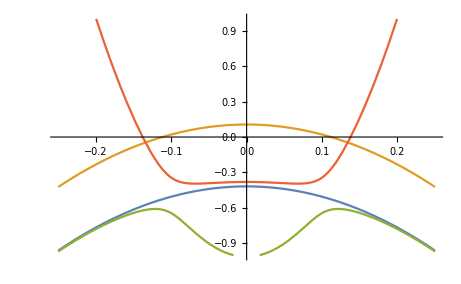

```mathematica
ClearAll["Global`*"]
H=({{e10+e11 kx^2+e12 ky^2+e13 kz^2, -2 ⅈ a121 ky+2 b121 kx kz, a130 + b131 kx^2+b132 ky^2+b133 kz^2, 4 ⅈ b142 kx ky+a142 kz+(2 c141+c143) kx^2 kz+(-2 c141+c143) ky^2 kz+c144 kz^3}, {2 ⅈ a121 ky+2 b121 kx kz, e20+e21 kx^2+e22 ky^2+e23 kz^2, -2 ⅈ a231 ky+2 b231 kx kz, 2 a241 kx+2 ⅈ b241 ky kz}, {a130+b131 kx^2+b132 ky^2+b133 kz^2, 2 ⅈ a231 ky+2 b231 kx kz, e30+e31 kx^2+e32 ky^2+e33 kz^2, 4 ⅈ b342 kx ky+a342 kz}, {4 ⅈ b142 kx ky-a142 kz+(-2 c141-c143) kx^2 kz+(2 c141-c143) ky^2 kz-c144 kz^3, -2 a241 kx+2 ⅈ b241 ky kz, 4 ⅈ b342 kx ky-a342 kz, e40+e41 kx^2+e42 ky^2+e43 kz^2}});

ky=0;kz=0;
{e10,e20,e30,e40}={-0.976,-0.418,-0.054,0.106};
{e11,e21,e31,e41}={49.26,-8.7,-28.7,-8.46};
{a130,b131,a241}={0.15,0,0.49};
MatrixForm[H]
Bd=Eigenvalues[H];
XGX=Plot[{Bd[[1]],Bd[[2]],Bd[[3]],Bd[[4]]},{kx,-0.25,0.25},PlotRange->{-1,1}];
Show[XGX]
```

## Assignments:

### (Sm B_6)

### (Hg Cr_2 Se_4)

## 2, Magnetic Field Applied

## 3, Strain Applied